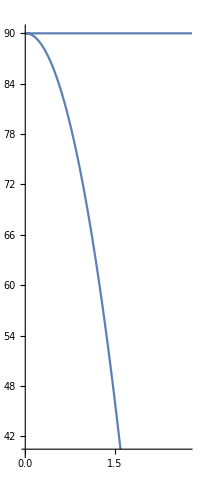

```mathematica
f1[t_] := t/2;
f2[t_] := 90+t/5-9.8*t^2/2;
(*Animate[ParametricPlot[{f1[t], f2[t]},{t, 0, tt}], {tt, 0, 3.2}]*)
ParametricPlot[{f1[t], f2[t]},{t, 0, 3.2}]
```

```mathematica
Integrate[Sqrt[f1'[t]^2+f2'[t]^2],{t}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {t}.

```mathematica
Integrate[-9.8,t]
```

-9.8 t

```mathematica
f1[t_] := 3*Cos[t]+ Cos[3*t];
f2[t_] := 3*Sin[t] - Sin[3*t];
curves = ParametricPlot[{f1[t], f2[t]}, {t,0, 2*Pi}];
Animate[
Show[
curves,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,2 Pi}]
integral = Integrate[2*Pi*f2[t]*Sqrt[f1'[t]^2+f2'[t]^2], {t, 0, pi}];
Real[integral]
```

Real[ConditionalExpression[48/5 π Sin[pi]^3 √(Sin[2 pi]^2) Tan[pi], 2 Re[pi]≤π||pi∉ℝ]]

```mathematica
f1[t_] := Cos[2*Pi*t];
f2[t_] := Sin[2*Pi*t];
curves2 = ParametricPlot[{f1[t], f2[t]}, {t,0, 1/2}];
Animate[
Show[
curves2,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,1/2}]
```

```mathematica
f1[t_] := Cos[2*Pi*t^2];
f2[t_] := Sin[2*Pi*t^2];
curves3 = ParametricPlot[{f1[t], f2[t]}, {t,0, 1/2}];
Animate[
Show[
curves3,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,1/2}]
```

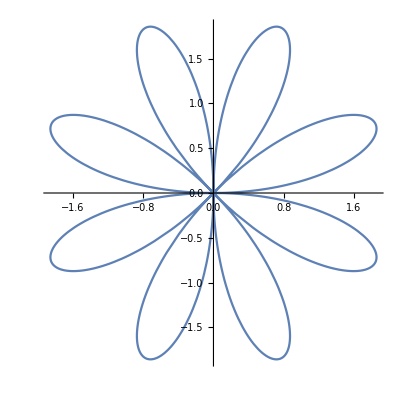

```mathematica
PolarPlot[2*Sin[4*t], {t,0, 2*Pi}]
```

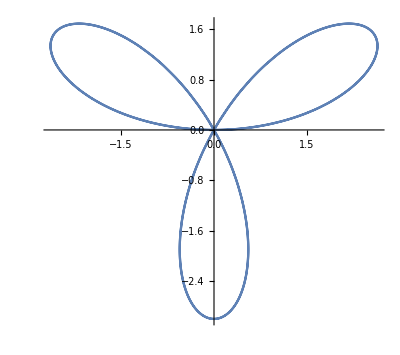

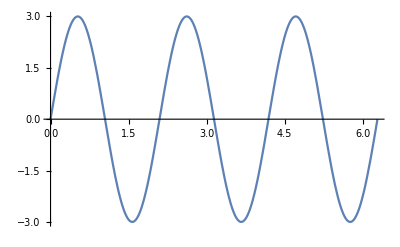

```mathematica
PolarPlot[3*Sin[3*t], {t,0, 2*Pi}]
Plot[3*Sin[3*t], {t,0, 2*Pi}]
```

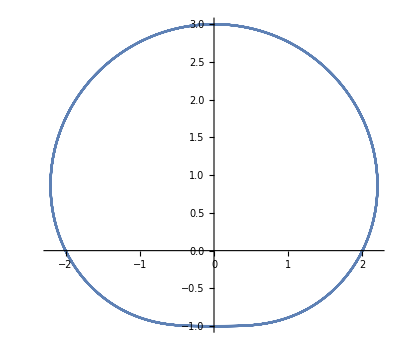

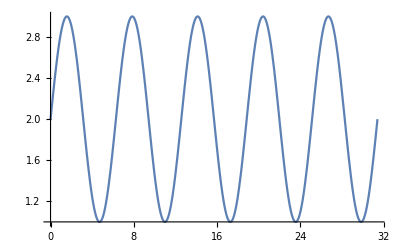

```mathematica
ff1[t_] := 2+Sin[t]
PolarPlot[ff1[t], {t,0, 10*Pi}]
Plot[ff1[t], {t,0, 10*Pi}]
```

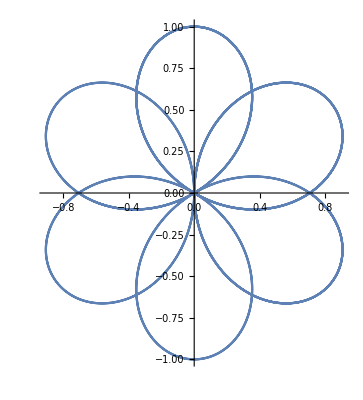

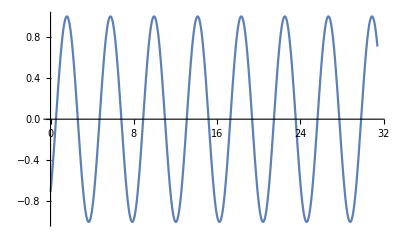

```mathematica
ff2[t_] := Sin[3*t/2-Pi/4]
PolarPlot[ff2[t], {t,0, 10*Pi}]
Plot[ff2[t], {t,0, 10*Pi}]
```

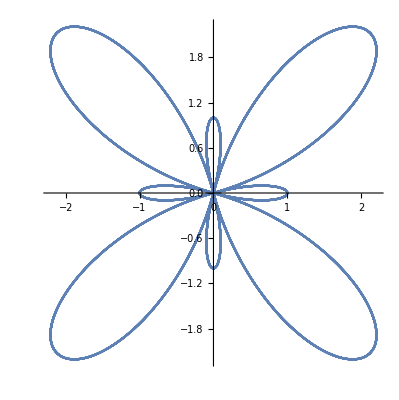

-Graphics-

```mathematica
ff3[t_] := -1+2*Cos[4*t]
PolarPlot[ff3[t], {t,0, 10*Pi}]
Plot[f3[t], {t,0, 10*Pi}]
```

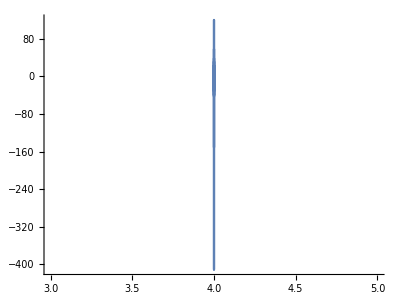

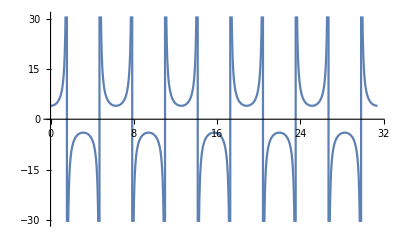

```mathematica
ff4[t_] := 4/Cos[t]
PolarPlot[ff4[t], {t,0, 10*Pi}]
Plot[ff4[t], {t,0, 10*Pi}]
```

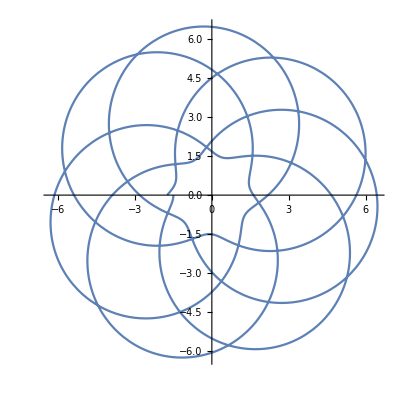

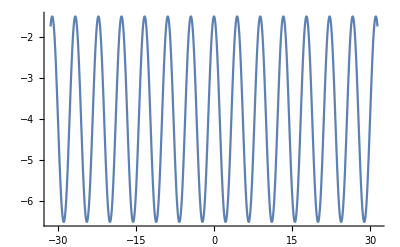

```mathematica
ff5[t_] := -4+2.5*Cos[Sqrt[2]*t]
PolarPlot[ff5[t], {t,0, 10*Pi}]
Plot[ff5[t], {t,-10*Pi, 10*Pi}]
```

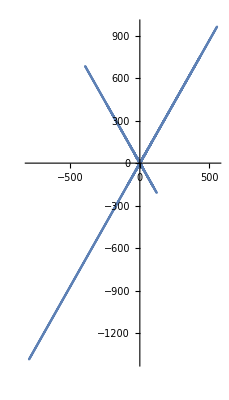

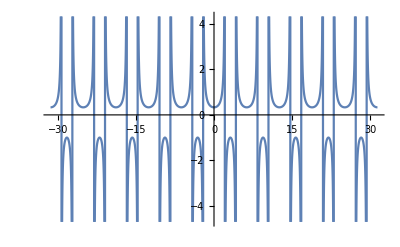

```mathematica
ff6[t_] := 1/(1+2*Cos[t])
pp6 = PolarPlot[ff6[t], {t,-10*Pi, 10*Pi}]
Plot[ff6[t], {t,-10*Pi, 10*Pi}]
Animate[
Show[
pp6,
Graphics[{PointSize[Large],Point[{ff6[t]*Cos[t],ff6[t]*Sin[t]}]}]
],{t,-10*Pi,10* Pi}]
```

```mathematica
Manipulate[{b,PolarPlot[1/(1+b*Cos[t]), {t,-10*Pi, 10*Pi}]},{b,-10,10}]
```

0.5

0.5

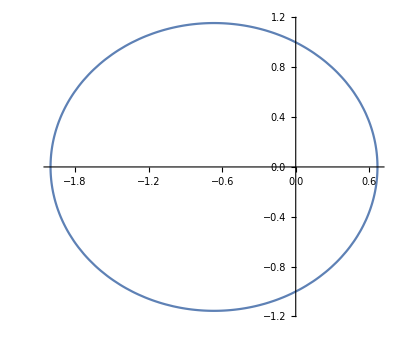

```mathematica
b = 0.5
Print[b]
PolarPlot[1/(1+b*Cos[t]), {t,0, 2*Pi}]
```

Set::write: Tag Sqrt in √0.99999 is Protected.

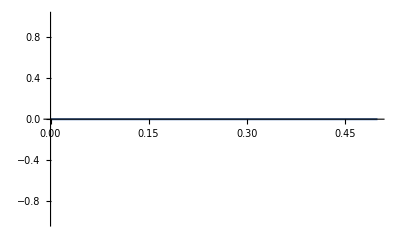

```mathematica
Plot[Sqrt[1-x-3/4*x^2]=0, {x, -2,0.5}]
```

```mathematica
kk = 3;
fg1[t_] := Cosh[t];
fg2[t_] := Sinh[t];
curvesfg = ParametricPlot[{fg1[t], fg2[t]}, {t,-1/2*Pi, 1/2*Pi}];
Animate[
Show[
curvesfg,
Graphics[{PointSize[Large],Point[{fg1[t],fg2[t]}]}]
],{t,-1/2*Pi,Pi/2}]
```

Set::write: Tag Plus in x^2-y^2 is Protected.

Solve::naqs: 1 is not a quantified system of equations and inequalities.

Solve[1,y]

```mathematica
ToPolarCoordinates[{-1,6}]
```

{√37,π-ArcTan[6]}

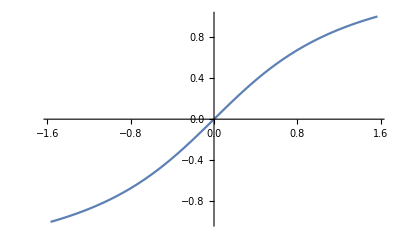

```mathematica
Plot[ArcTan[x], {x, -Pi/2,Pi/2}]
```

```mathematica
rd1[t_1] :=aa+bb*Cos[t];
fdx[t_] := rd1[t]*Cos[t];
fdy[t_] := rd1[t]*Sin[t];
Simplify[Sqrt[fdx'[t]^2+fdy'[t]^2]]
```

√(aa^2+bb^2+2 aa bb Cos[t])

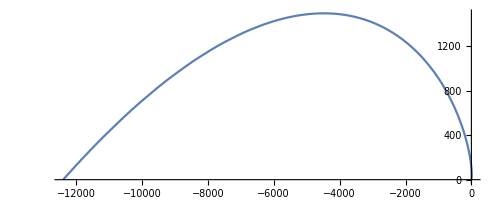

```mathematica
PolarPlot[Exp[3*t], {t,0, Pi}]
```

```mathematica
Integrate[1/2*Exp[6*t],{t, 0, Pi}]
```

1/12 (-1+ⅇ^(6 π))

{2 EllipticE[1/2],Double[2 EllipticE[1/2]]}

```mathematica
kk=1;Integrate[2*kk*Sqrt[Sin[t]^(2*(kk-1))*Cos[t]^2+Cos[t]^(2*(k-1))*Sin[t]^2], {t, 0, Pi/2}];
```

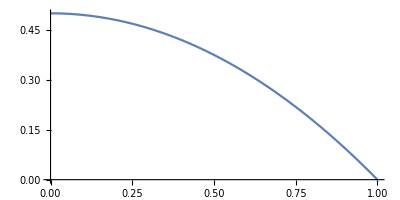

```mathematica
PolarPlot[1/(1+Sin[t]), {t,0, Pi/2}]
```

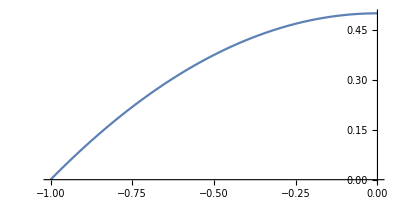

```mathematica
PolarPlot[1/(1+Sin[t]), {t,Pi/2, Pi}]
```

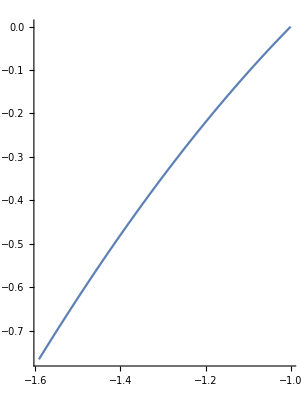

```mathematica
PolarPlot[1/(1+Sin[t]), {t,Pi, 8*Pi/7}]
```

```mathematica
Solve[xx^2-yy^2==1, yy]
```

{{yy→-√(-1+xx^2)},{yy→√(-1+xx^2)}}

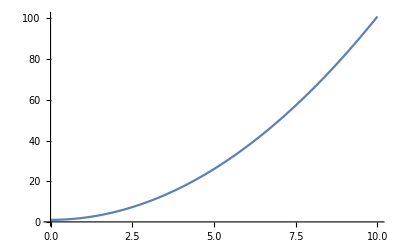

```mathematica
plot = Plot[x^2+1, {x, 0, 10}]
```

```mathematica
Simplify[Integrate[1/Sqrt[1+t^2],{t, 0, x}]-ArcSinh[x/(√(1+x^2))]]
Simplify[D[ArcTanh[x/(√(1+x^2))],x]]
```

```mathematica
Simplify[-ArcSinh[x]+ArcTanh[x/(√(1+x^2))]]
```

-ArcSinh[x]+ArcTanh[x/(√(1+x^2))]

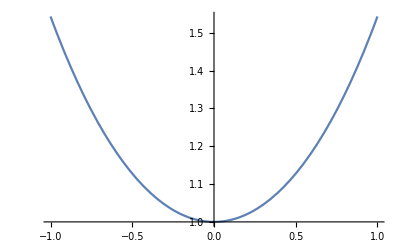

```mathematica
Plot[Cosh[x], {x, -1, 1}]
```

```mathematica
Manipulate[{b,PolarPlot[1/(1+b*Cos[t]), {t,-10*Pi, 10*Pi}]},{b,-10,10}]
```